# Linux - ILOCI Test 7 Training and Verification to build Classify file “ILOCITest7Classifier.m”

```mathematica
trainingfile="/home/pi/Mathematica/ILOCITrainingFile.m"
```

/home/pi/Mathematica/ILOCITrainingFile.m

```mathematica
datafile ="/home/pi/Mathematica/2016_6_25_28.dat"
```

/home/pi/Mathematica/2016_6_25_28.dat

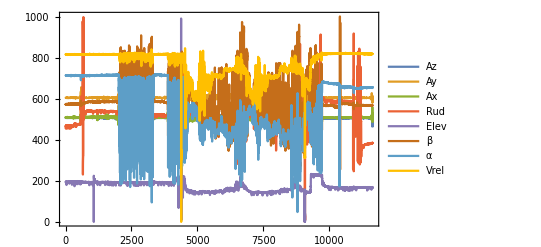

```mathematica
descriptionfile = datafile<>".txt";description = Import[descriptionfile,"List"];dataseconds = description[[3]]-description[[1]];
datausecs = description[[4]]-description[[2]];
npoints=description[[5]];
frametime = (dataseconds*1.0*^6+datausecs)/npoints;
data = Import[datafile];
plotdata = Transpose[data];
ListLinePlot[plotdata,PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Manipulate[
 ListPlot[plotdata, PlotRange -> {{ts, te}, {low, high}}, AxesOrigin -> {ts, low}, GridLines -> Automatic, Joined -> True],
 {ts, 0.0, npoints, npoints/100.0}, {{te, npoints}, ts, npoints, npoints/100}, {low, 0, 1024, 100}, {{high, 1024}, low, 1024, 100}]

## ground no LOC sets - noloc1 to noloc8

### Ground stationary noloc1- noloc2, nloc9

ground engine off

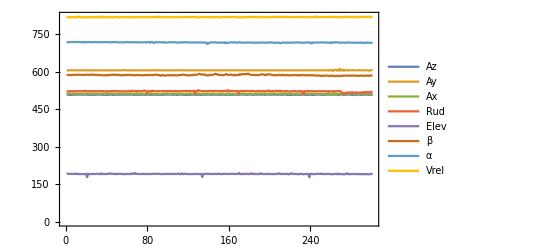

```mathematica
noloc1=Take[data,{3500,3800}];ListLinePlot[Transpose[noloc1],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

ground engine running

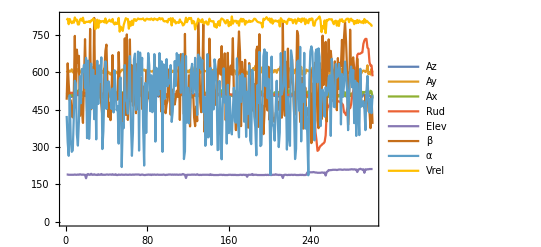

```mathematica
noloc2=Take[data,{3900,4200}];ListLinePlot[Transpose[noloc2],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

roll out

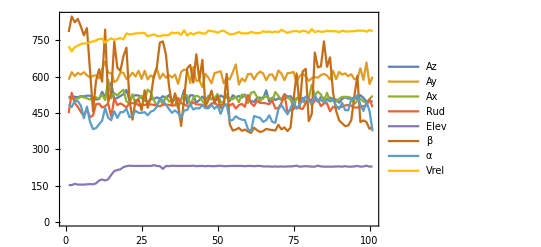

```mathematica
noloc9=Take[data,{9300,9400}];ListLinePlot[Transpose[noloc9],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

### Airborne noloc3 to noloc8

takeoff,  climb at 60 knots

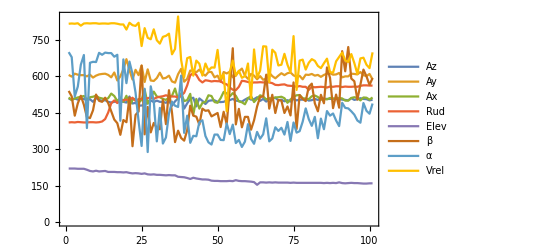

```mathematica
noloc3=Take[data,{4500,4600}];ListLinePlot[Transpose[noloc3],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Verification set is takeoff to climb at 60

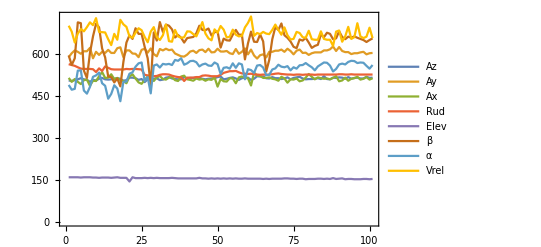

```mathematica
nolocV3=Take[data,{4600,4700}];ListLinePlot[Transpose[nolocV3],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Climb at 70 knots

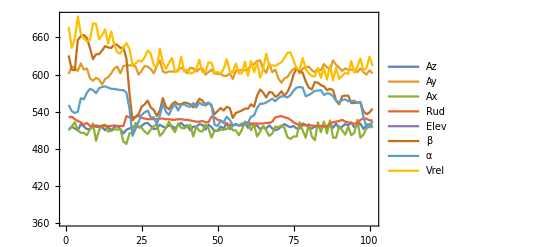

```mathematica
noloc4=Take[data,{4800,4900}];ListLinePlot[Transpose[noloc4],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

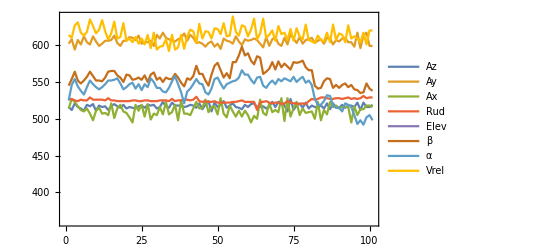

```mathematica
nolocV4=Take[data,{4900,5000}];ListLinePlot[Transpose[nolocV4],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Climb at 50 kn

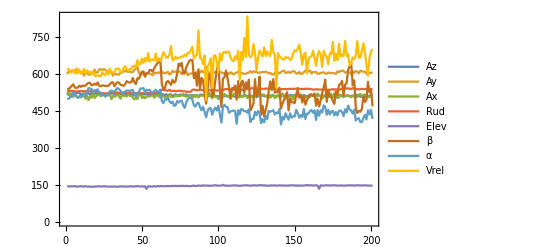

```mathematica
noloc5=Take[data,{5000,5200}];ListLinePlot[Transpose[noloc5],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Verification at 50Knots to motor off

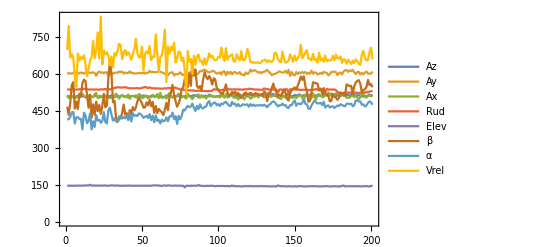

```mathematica
nolocV5=Take[data,{5200,5400}];ListLinePlot[Transpose[nolocV5],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Glide at 42 knots

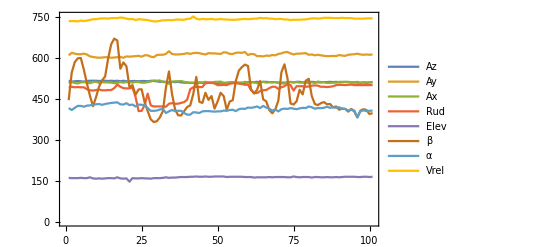

```mathematica
noloc6=Take[data,{6200,6300}];ListLinePlot[Transpose[noloc6],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

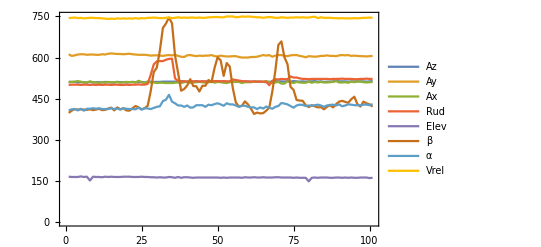

```mathematica
nolocV6=Take[data,{6300,6400}];ListLinePlot[Transpose[nolocV6],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Engine on, climb at 60kn, then 70kn

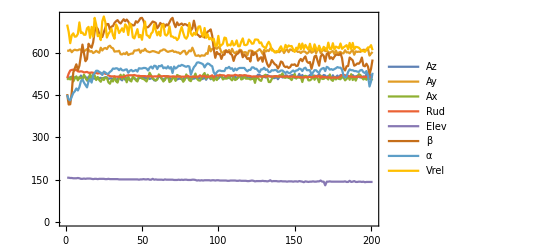

```mathematica
noloc7=Take[data,{6900,7100}];ListLinePlot[Transpose[noloc7],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

verification at 70kn to 50kn

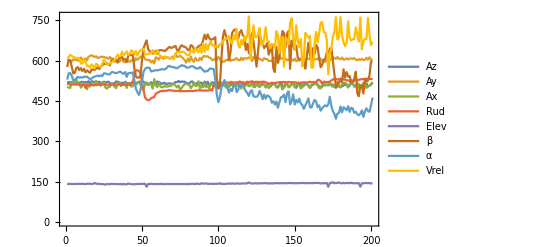

```mathematica
nolocV7=Take[data,{7100,7300}];ListLinePlot[Transpose[nolocV7],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Landing power on

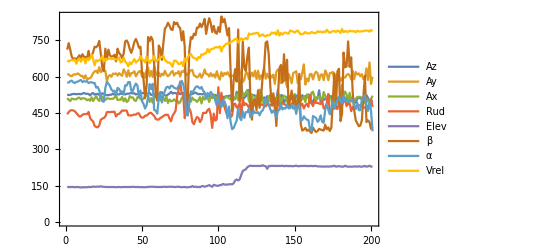

```mathematica
noloc8=Take[data,{9200,9400}];ListLinePlot[Transpose[noloc8],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Verification is rollout

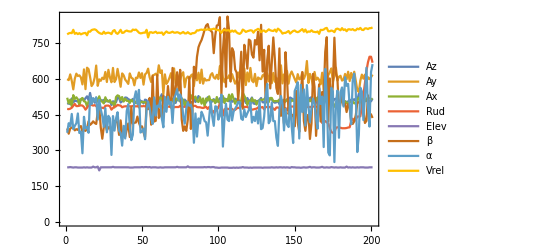

```mathematica
nolocV8=Take[data,{9400,9600}];ListLinePlot[Transpose[nolocV8],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

## LOC sets loc1 to loc4

### stalls straight, Left turn, right turn

straight stall

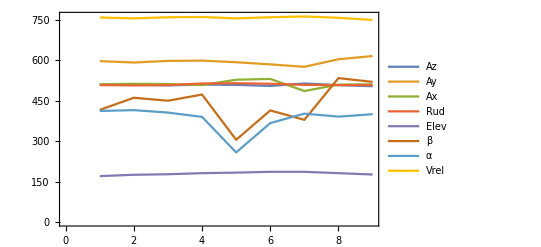

```mathematica
loc1=Take[data,{6450,6458}];ListLinePlot[Transpose[loc1],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Left stall

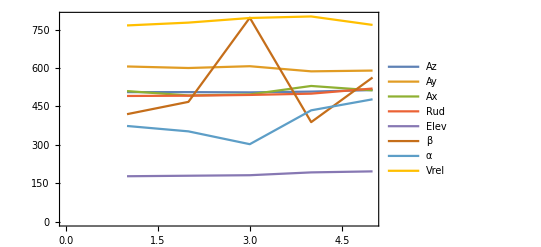

```mathematica
loc2=Take[data,{6480,6484}];ListLinePlot[Transpose[loc2],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

right stall

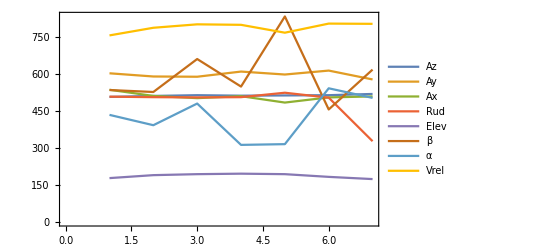

```mathematica
loc3=Take[data,{6528,6534}];ListLinePlot[Transpose[loc3],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Use the 2nd straight stall

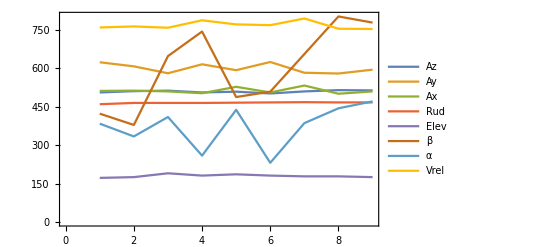

```mathematica
locV1=Take[data,{6587,6595}];ListLinePlot[Transpose[locV1],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

### Yaw Loc Sets

Right Yaw

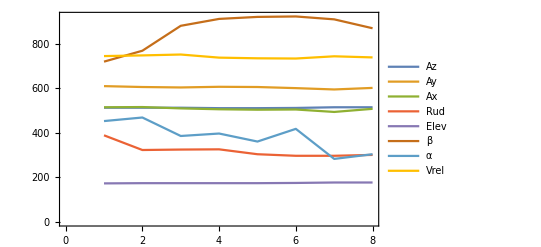

```mathematica
loc4=Take[data,{6693,6700}];ListLinePlot[Transpose[loc4],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Left Yaw

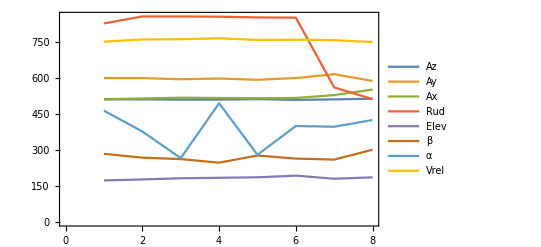

```mathematica
loc5=Take[data,{6720,6727}];ListLinePlot[Transpose[loc5],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Verification uses 2nd Right Yaw

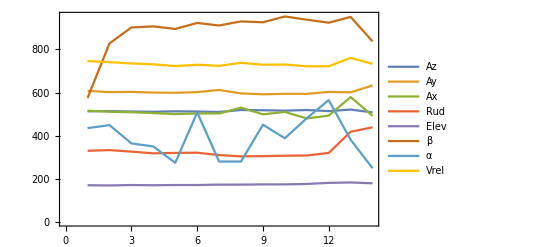

```mathematica
locV2=Take[data,{6763,6776}];ListLinePlot[Transpose[locV2],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},Frame->True]
```

Glide to Vne - Not performed for Test 7

loc6 = Take[data, {8030, 8055}]; ListLinePlot[Transpose[loc6]]

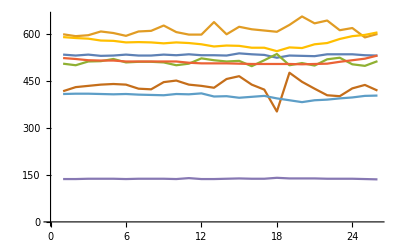

## Training sets to give Classes for Responses

Normal response “N” for cases noloc3 to noloc9
Stall Response  “D” for cases loc1, loc2, loc3
Yaw response “L” for cases loc4
Yaw response “R” for cases loc5
Dive response “U” for loc6 - not performed for Test7

### Normal response “N” for cases noloc to noloc8

normal = Join[noloc1, noloc2, noloc3, noloc4, noloc5, noloc6, noloc7, noloc8, noloc9];

If we leave out noloc9, which was the long roll out we get better results?

```mathematica
normal = Join[noloc1,noloc2,noloc3,noloc4,noloc5,noloc6,noloc7,noloc8];
```

```mathematica
normalRule=Rule[#1,"N"]&;
```

```mathematica
normalpairs= normalRule/@normal;
```

```mathematica
Length[normalpairs]
```

1508

### Stall response “D” for cases loc1, loc2,loc3

define a function that repeats a short length case n times, so that when we train Classify, the LOC cases have somewhat similar weights compared to the normal cases

```mathematica
amplification = 10;
```

```mathematica
amplify[p_]:=Module[{res},res={};Do[AppendTo[res,p],{i,1,amplification}];Flatten[res,1]]
```

```mathematica
down = amplify[Join[loc1,loc2,loc3]];
```

```mathematica
downRule=Rule[#1,"D"]&;
```

```mathematica
downpairs= downRule/@down;
```

```mathematica
Length[downpairs]
```

210

### Yaw response “L” for cases loc4

```mathematica
left = amplify[loc4];
```

```mathematica
leftRule=Rule[#1,"L"]&;
```

```mathematica
leftpairs= leftRule/@left;
```

```mathematica
Length[leftpairs]
```

80

### Yaw response “R” for cases loc5

```mathematica
right = amplify[loc5];
```

```mathematica
rightRule=Rule[#1,"R"]&;
```

```mathematica
rightpairs= rightRule/@right;
```

```mathematica
Length[rightpairs]
```

80

Dive response “U” for cases loc6 - not performed for Test7

up = amplify[loc6];

upRule = Rule[#1, "U"] &;

uppairs = upRule /@ up;

Length[uppairs]

10

### Define rules to extract probabilities for each class

```mathematica
pN=classify[#,"Probabilities"][[3]]&;
```

```mathematica
pD=classify[#,"Probabilities"][[1]]&;
```

```mathematica
pL=classify[#,"Probabilities"][[2]]&;
```

```mathematica
pR=classify[#,"Probabilities"][[4]]&;
```

pU = classify[#, "Probabilities"][[5]] &;

## Train the 5 classes N, D, R, L, U

```mathematica
trainingsets = Join[normalpairs,downpairs,rightpairs,leftpairs];
Length[trainingsets]
```

1878

#### save the trainingsets for later use with updates

```mathematica
Put[trainingsets,trainingfile]
```

#### Use a neural network classifier, that seems to give best results

```mathematica
classify = Classify[trainingsets, Method -> {"NeuralNetwork", PerformanceGoal -> "Quality"}]
```

ClassifierFunction[…]

classify = Classify[trainingsets, Method -> {"NeuralNetwork", "HiddenLayers" -> {160}}, PerformanceGoal -> "Quality"]

classify = Classify[trainingsets, Method -> "SupportVectorMachine"]

```mathematica
ClassifierInformation[classify]
```

Classifier information
Method | Neural network
Number of classes | 4
Number of features | 8
Number of training examples | 1878
Number of extracted features | 8
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1
Number of hidden layers | 2
Hidden nodes | ,,2424
Hidden layer activation functions | ,,Rectified LinearRectified Linear

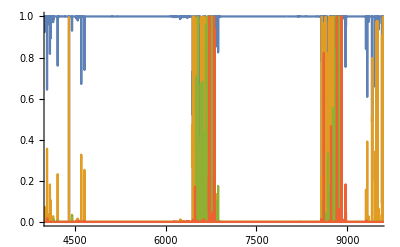

```mathematica
ListLinePlot[{pN/@data,pD/@data,pL/@data,pR/@data},PlotRange->{{4100,9500},Automatic}]
```

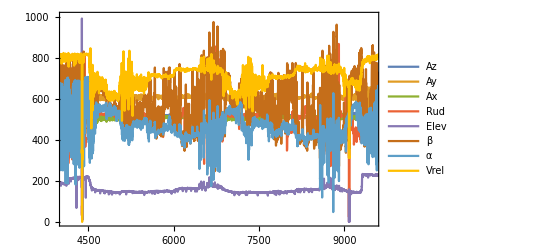

```mathematica
ListLinePlot[Transpose[data], PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"},PlotRange -> {{4100, 9500}, All},Frame->True]
```

### Did Classify properly train the training set?

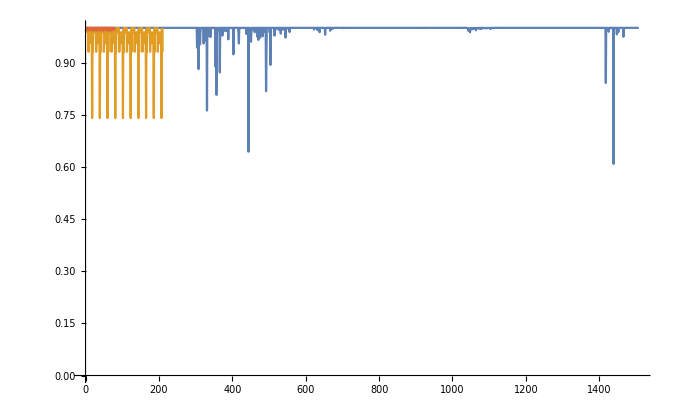

```mathematica
ListLinePlot[{pN/@normal,pD/@down,pL/@left,pR/@right},PlotRange->{Automatic,{0,1}}]
```

As long as they are always above 0.5, all cases were trained properly.  Class D was trained least

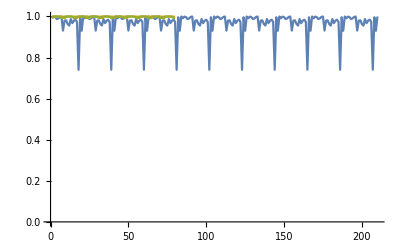

```mathematica
ListLinePlot[{pD/@down,pL/@left,pR/@right},PlotRange->{Automatic,{0,1}}]
```

### Can classify recognize the verification sets?

Normal nolocV3 -  nolocV8

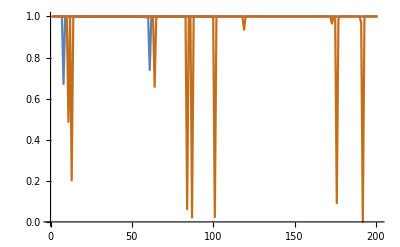

```mathematica
ListLinePlot[{pN/@nolocV3,pN/@nolocV4,pN/@nolocV5,pN/@nolocV6,pN/@nolocV7,pN/@nolocV8},PlotRange->{Automatic,{0,1}}]
```

nolocV8 is having trouble during roll out

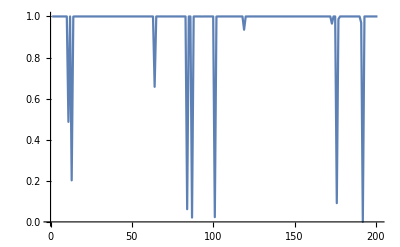

```mathematica
ListLinePlot[{pN/@nolocV8},PlotRange->{Automatic,{0,1}}]
```

```mathematica
classify[nolocV8]
```

{N,N,N,N,N,N,N,N,N,N,D,N,D,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,D,N,N,D,N,N,N,N,N,N,N,N,N,N,N,N,N,D,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,D,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,D,N,N,N,N,N,N,N,N,N}

Stall verification locV1

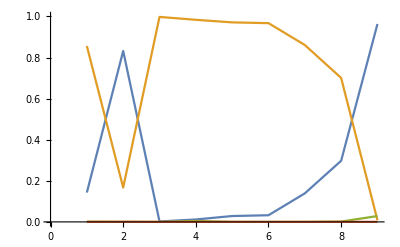

```mathematica
ListLinePlot[{pN/@locV1,pD/@locV1,pL/@locV1,pR/@locV1},PlotRange->{Automatic,{0,1}}]
```

Classify is recognizing an untrained stall correctly

Yaw verification locV2

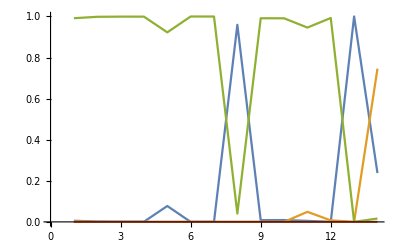

```mathematica
ListLinePlot[{pN/@locV2,pD/@locV2,pL/@locV2,pR/@locV2},PlotRange->{Automatic,{0,1}}]
```

```mathematica
classify[locV2]
```

{L,L,L,L,L,L,L,N,L,L,L,L,N,D}

## Apply the classifier to the second flight period, when LOC was imminent

Actual flight

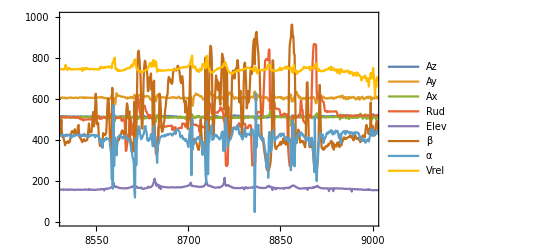

```mathematica
ListLinePlot[Transpose[data],PlotLegends->{"Az","Ay","Ax","Rud","Elev","β","α","Vrel"}, PlotRange -> {{8500, 9000}, All},Frame->True]
```

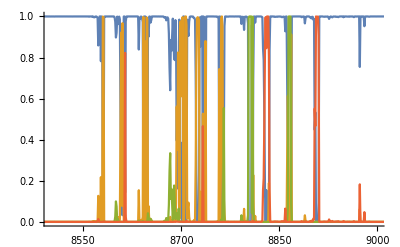

```mathematica
ListLinePlot[{pN/@data,pD/@data,pL/@data,pR/@data},PlotRange->{{8500,9000},Automatic}]
```

## Save the classifier

The trained network can be saved in Mathematica  for future use before it is removed.

```mathematica
classifierfile="/home/pi/Mathematica/"<>"ILOCITest7Classifier.m"
```

/home/pi/Mathematica/ILOCITest7Classifier.m

#### Putting out the classifier writes a list with all the classifier values, which can be read in as a list, and used as a renamed classifier

```mathematica
Put[classify,classifierfile]
```

#### Verify we can read the saved classifier

```mathematica
c=Get[classifierfile]
```

ClassifierFunction[…]